```mathematica
Clear["Global`*"]
```

```mathematica
inputData = Import[NotebookDirectory[]<>"/input.txt"];
input = StringSplit[inputData];
l=Length[input];(*l will have to be even*)
(*Write a function here that will take in strings as variable names*)
dt=Read[StringToStream[input[[2]]]];
tmax=input[[4]];
nTrajectory=input[[6]];
nstore=input[[8]];
yWall=input[[10]];
sigmaXX=input[[12]];
sigmaXZ=input[[14]];
transitTime=input[[16]];
sigmaPX=input[[18]];
sigmaPY=input[[20]];
sigmaPZ=input[[22]];
density=input[[24]];
rabi=input[[26]];
kappa=input[[28]];
name =input[[30]]
```

latt_tau1.0_g2_k40_N100

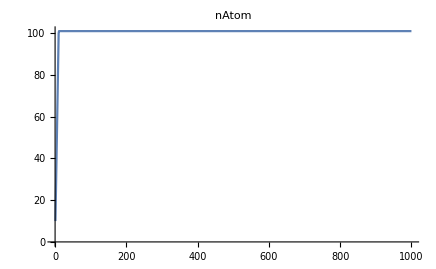

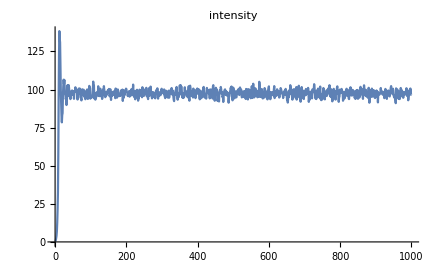

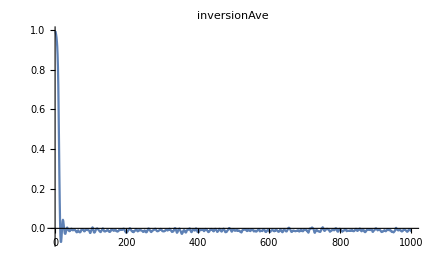

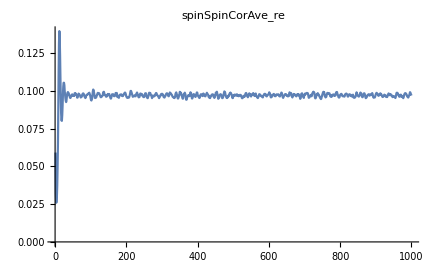

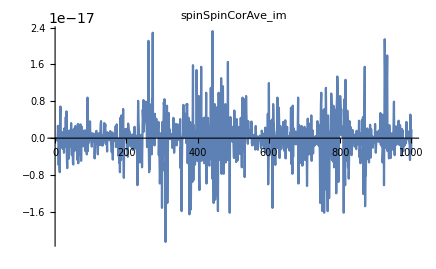

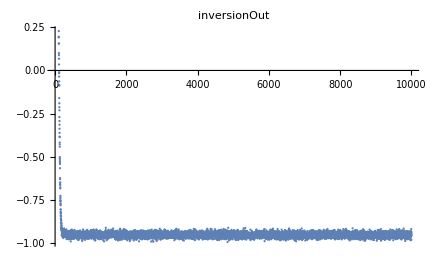

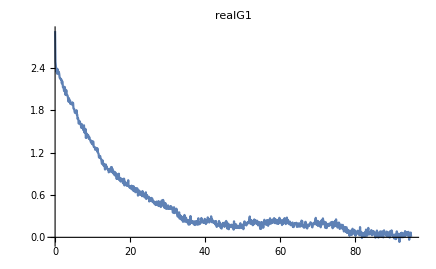

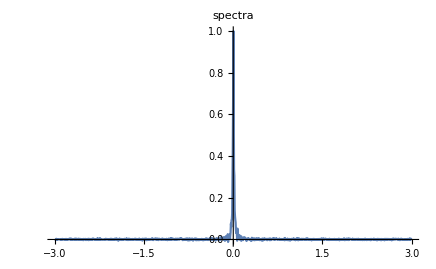

```mathematica
(*When doing one run*)
intensity=Flatten[Import[NotebookDirectory[]<>name<>"/intensity.dat"]];
nAtom=Flatten[Import[NotebookDirectory[]<>name<>"/nAtom.dat"]];
inversionAve=Flatten[Import[NotebookDirectory[]<>name<>"/inversionAve.dat"]];
spinSpinCorAveRe=Flatten[Import[NotebookDirectory[]<>name<>"/spinSpinCorAve_re.dat"]];
spinSpinCorAveIm=Flatten[Import[NotebookDirectory[]<>name<>"/spinSpinCorAve_im.dat"]];
szFinal=Flatten[Import[NotebookDirectory[]<>name<>"/szFinal.dat"]];
realG1 = Import[NotebookDirectory[]<>name<>"/realG1.dat"];
spectra=Import[NotebookDirectory[]<>name<>"/spectra.dat"];
ListLinePlot[nAtom,PlotRange->All,PlotLabel->"nAtom"]
ListLinePlot[intensity,PlotRange->All,PlotLabel->"intensity"]
ListLinePlot[inversionAve,PlotRange->All,PlotLabel->"inversionAve"]
ListLinePlot[spinSpinCorAveRe,PlotRange->All,PlotLabel->"spinSpinCorAve_re"]
ListLinePlot[spinSpinCorAveIm,PlotRange->All,PlotLabel->"spinSpinCorAve_im"]
ListPlot[szFinal,PlotRange->All,PlotLabel->"inversionOut"]
ListLinePlot[realG1,PlotRange->All,PlotLabel->"realG1"]
ListLinePlot[spectra,PlotRange->All,PlotLabel->"spectra"]
```

FittedModel[0.000345696/(0.000391376+4 x^2)]

| Estimate | Standard Error | t-Statistic | P-Value
linewidth | 0.0197832 | 0.000254615 | 77.6986 | 2.45892122696×10^-457
A | 0.0174742 | 0.000158379 | 110.332 | 4.5681487972×10^-610

0.0197832

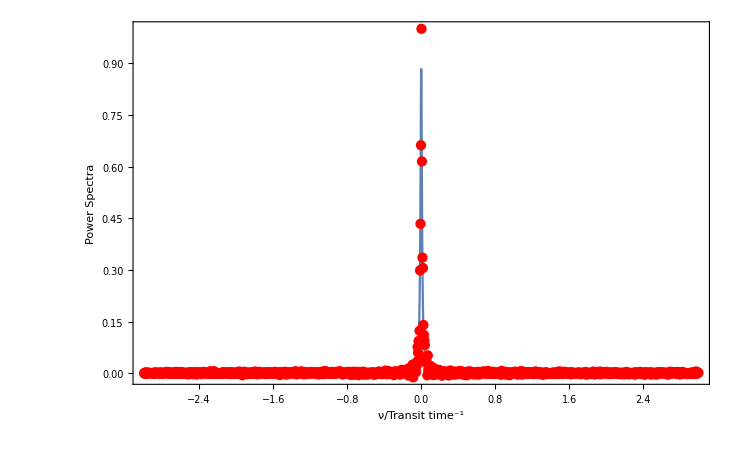

```mathematica
(*Fit the spectra to lorentzian*)
lorentzianModel=A linewidth/(linewidth^2+4x^2);
fitLoren=NonlinearModelFit[spectra,{lorentzianModel},{linewidth,A},{x}]
fitLoren["ParameterTable"]
linewidth1 = linewidth/.fitLoren["BestFitParameters"]
Show[{Plot[fitLoren[x],{x,-0.3,0.3},PlotRange->All,BaseStyle->{FontSize->30}],Graphics[{Red,PointSize[.01],Map[Point,spectra]}]},Frame->True,FrameLabel->{"ν/Transit time^-1","Power Spectra"}]
```

```mathematica
tauc1=1/(linewidth1 Pi)
```

16.0899

B ⅇ^(-t/tc)

FittedModel[2.38506 ⅇ^(-0.0573731 t)]

| Estimate | Standard Error | t-Statistic | P-Value
tc | 17.4298 | 0.131428 | 132.618 | 9.07073955269×10^-615
B | 2.38506 | 0.0126723 | 188.21 | 1.11576898343×10^-753

17.4298

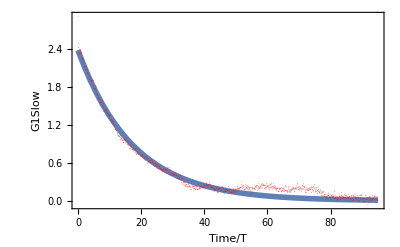

```mathematica
(*Fit the G1 function to exponential*)
exponentialModel=B Exp[- t/tc]
fitExp=NonlinearModelFit[realG1,{exponentialModel},{tc,B},{t}]
fitExp["ParameterTable"]
tauc2=tc/.fitExp["BestFitParameters"]
Show[{Plot[fitExp[x],{x,0,Last[realG1][[1]]},PlotRange->All,PlotStyle->{Thickness[0.01]},BaseStyle->{FontSize->30}],Graphics[{Red,PointSize[.001],Map[Point,realG1]}]},Frame->True,FrameLabel->{"Time/T","G1Slow"}]
```

```mathematica
(*Get the linewidth from the coherent time*)
linewidth2 = 1/(tauc2 Pi)
```

0.0182624

```mathematica
(*Notice there is another exponential decay.*)
```

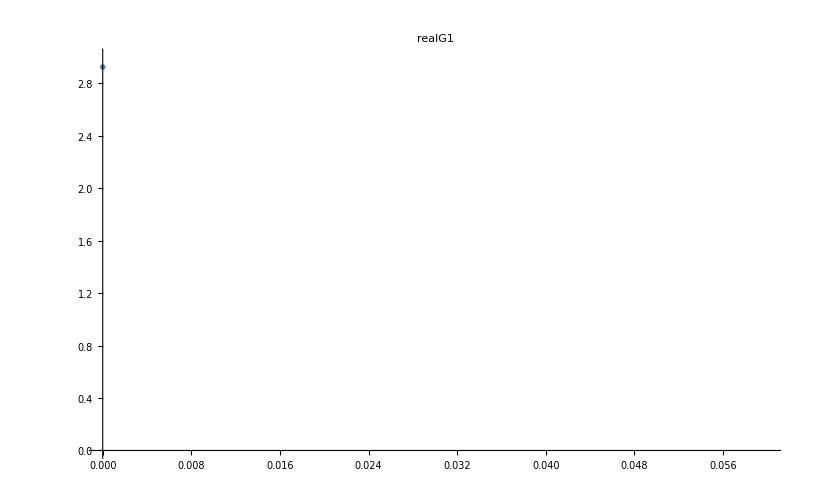

B2 ⅇ^(-linewidthQuick π t)

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

NonlinearModelFit[{},{B2 ⅇ^(-linewidthQuick π t)},{linewidthQuick,B2},{t}]

NonlinearModelFit[{},{B2 ⅇ^(-linewidthQuick π t)},{linewidthQuick,B2},{t}][ParameterTable]

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

-Graphics-

```mathematica
cutOff = 0.06;
ListPlot[realG1,PlotRange->{{0,cutOff},{0,3}}, 
PlotLabel->"realG1",PlotMarkers->{Automatic,Small}]
secondNum=IntegerPart[cutOff/realG1[[2,1]]];
secondExp=Take[realG1,secondNum];
exponentialModel2=B2 Exp[- Pi linewidthQuick t]
fitExp2=NonlinearModelFit[secondExp,{exponentialModel2},{linewidthQuick,B2},{t}]
fitExp2["ParameterTable"]
Show[{Plot[fitExp2[x],{x,0,cutOff},PlotRange->All,BaseStyle->{FontSize->30}],Graphics[{Red,PointSize[.02],Map[Point,secondExp]}]},Frame->True,FrameLabel->{"Time/T","G1Fast"}]
```

```mathematica
secondTc = 1/(linewidthQuick Pi)/.fitExp2["BestFitParameters"]
```

ReplaceAll::reps: {NonlinearModelFit[{},{B2 ⅇ^(-linewidthQuick π t)},{linewidthQuick,B2},{t}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

1/(linewidthQuick π)/.NonlinearModelFit[{},{B2 ⅇ^(-linewidthQuick π t)},{linewidthQuick,B2},{t}][BestFitParameters]